```mathematica
(*Uniform下求解*)
```

```mathematica
Clear[basis,uh];
(*定义基函数*)
basis[n_,i_,x_]:=Module[{temp1=0,he=0},
he=1/n;
If[(i-1) he<x≤i he,temp1=(x-(i-1) he)/he,
If[i he<x<(i+1) he,temp1=((i+1) he-x)/he,
temp1=0]
];
temp1
];
(*定义离散数值解*)
uh[n_,ua_,x_]:=Module[{temp1=0,i,j,he=0},
he=1/n;
temp1=Sum[ua[[i]]*basis[n,i,x],{i,1,n-1}];
temp1
];
```

```mathematica
(*///////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////*)
```

```mathematica
(*epsilon=1e-7时均匀下结果*)
```

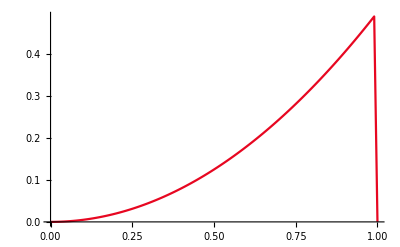

```mathematica
epsilon=1/10000000;
u[x_]:=(5000001 (1-ⅇ^(10000000 x)))/(10000000 (-1+ⅇ^10000000))+x/10000000+x^2/2;
(*真解函数*)
delta=N[1/100,50];
tablereal=Table[{i delta,u[i delta]},{i,0,100}];
img=ListLinePlot[tablereal,PlotStyle->ColorData[3,"ColorList"]]
```

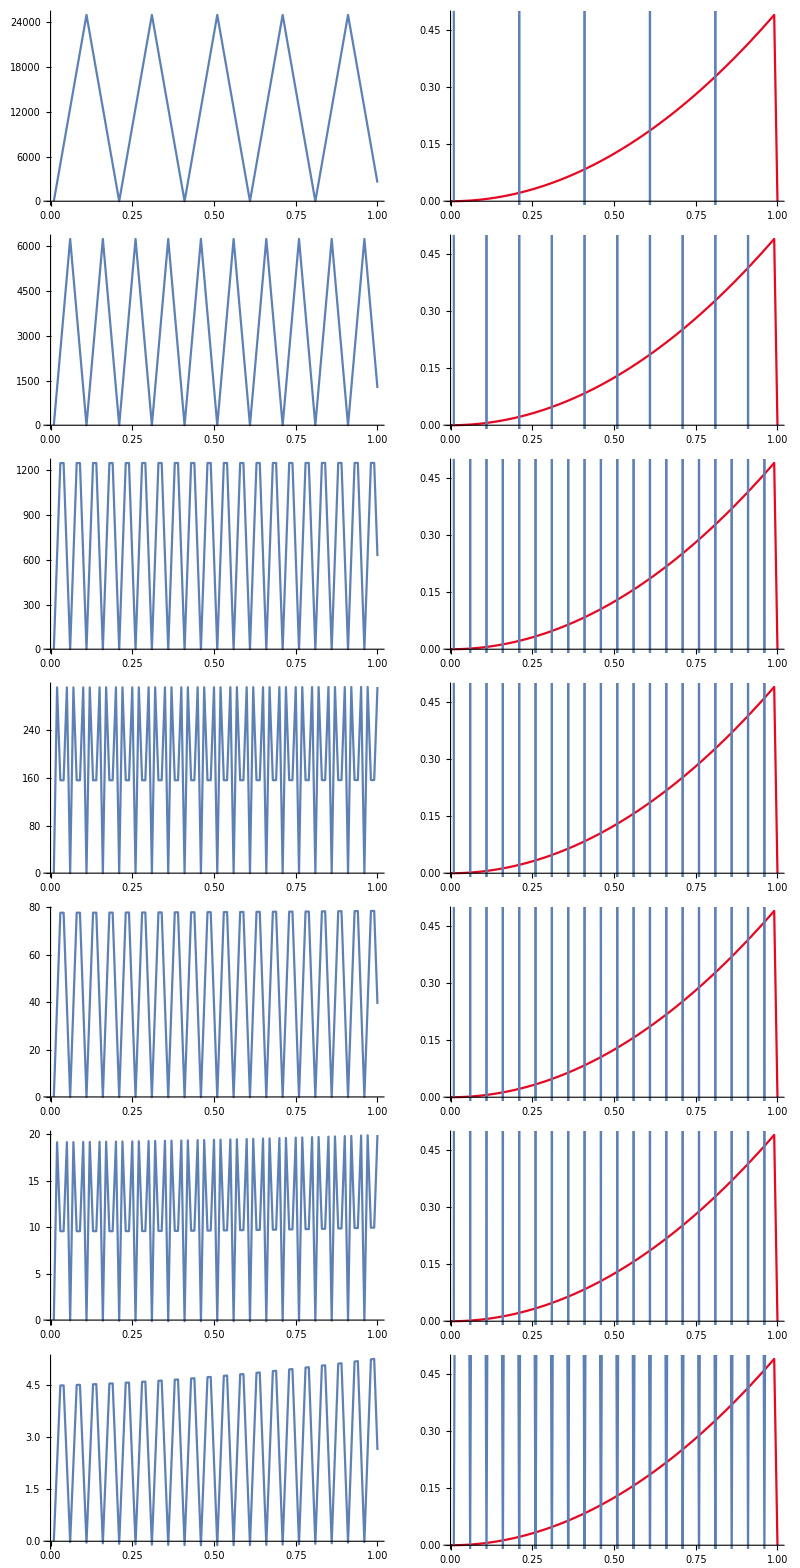
(-Graphics-)

```mathematica
(*记录误差*)
error=Table[{0,0,0,0},{i,7}];
imglist=Table[{0,0},{i,7}];
For[l=0,l<7,l++,
Clear[n,A,k];
(*离散程度*)
n=2^l*10;
he=1/n;
(*系数矩阵*)
A=Table[0,{i,n-1},{j,1,n-1}];
For[k=1,k<n-1,k++,
A[[k,k]]=2 epsilon /he;
A[[k,k+1]]=-epsilon/he+1/2;
A[[k+1,k]]=-epsilon/he-1/2;
];
k=n-1;
A[[k,k]]=2 epsilon /he;
(*右侧向量*)
fa=Table[i he^2,{i,1,n-1}];
(*求解方程组*)
ua=N[Inverse[N[A,50]].fa,50];
(*1000等分求解模最大误差*)
real=N[Table[u[i delta],{i,0,100}],50];
ns=Table[uh[n,ua,i delta],{i,0,100}];
error[[l+1,1]]=Max[Abs[N[real-ns,15]]];
(*生成相关图像*)
table=Table[{i delta,ns[[i]]},{i,0,100}];
img1=ListLinePlot[table];
imglist[[l+1,1]]=img1;
imglist[[l+1,2]]=Show[img,img1];
(*复化3点gauss求解L1范数误差*)
delta2=N[1/32,20];
xi=Table[m delta2,{m,0,32}];
error[[l+1,3]]=N[Sum[5/18 (xi[[i+1]]-xi[[i+1]])*Abs[u[(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,ua,(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]]+4/9 (xi[[i+1]]-xi[[i]])*Abs[u[(xi[[i+1]]+xi[[i]])/2]-uh[n,ua,(xi[[i+1]]+xi[[i]])/2]]+5/18 (xi[[i+1]]-xi[[i]])*Abs[u[(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,ua,(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]],{i,1,32}],15]
]
imglist//MatrixForm
```

```mathematica
(*求收敛阶*)
For[l=2,l≤7,l++,  
error[[l,2]]=Log[error[[l-1,1]]/error[[l,1]]]/Log[2];
error[[l,4]]=Log[error[[l-1,3]]/error[[l,3]]]/Log[2]];
list=Table[{10 2^i,error[[i+1,1]],error[[i+1,2]],error[[i+1,3]],error[[i+1,4]]},{i,0,6}];
list[[1,3]]="-";
PrependTo[list,{"n","无穷范数误差","Order","L1范数误差","Order"}];
GridBox[list,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | 无穷范数误差 | Order | L1范数误差 | Order
10 | 24999.95500239 | - | 9027.59807320872 | 0
20 | 6249.97626139496 | 2.0000028829058 | 2256.7623264936 | 2.0000877008286
40 | 1249.89534101884 | 2.3220434131177 | 564.053556200987 | 2.0003504310667
80 | 312.395239296385 | 2.0003629240253 | 140.878863716453 | 2.0013769732567
160 | 78.0206761262807 | 2.00144406199 | 35.0847955445089 | 2.0055373177243
320 | 19.4314340898817 | 2.0054641213331 | 16.5930221315904 | 1.0802692830384
640 | 4.78696695677027 | 2.0212086268188 | 0.470311773842321 | 5.14081541266279

```mathematica
(*///////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////*)
```

```mathematica
(*Shinshkin下求解*)
```

```mathematica
(*定义n等分时基函数*)
Clear[shinshkinbasis,uh];
shinshkinbasis[n_,i_,left_,right_,x_]:=Module[{temp1=0,he=0},
he=(right-left)/n;
If[left+(i-1) he<x≤left+i he,temp1=(x-left-(i-1) he)/he,
If[left+i he<x<left+(i+1) he,temp1=(left+(i+1) he-x)/he,
temp1=0]
];
temp1
];
(*定义离散数值解*)
uh[n_,epsilon_,ua_,x_]:=Module[{temp1=0,temp2=0,i,j,he1=0,he2=0,tao=0},
tao=1-2 epsilon Log[n];
he1=tao/n;
he2=(1-tao)/n;
temp1=Sum[ua[[i]]*shinshkinbasis[n,i,0,tao,x]+ua[[i+n]]*shinshkinbasis[n,i,tao,1,x],{i,1,n-1}];
If[(n-1) he1<x≤tao,temp2=ua[[n]] (x-(n-1) he1)/he1,
If[tao<x<tao+he2,temp2=ua[[n]] (tao+he2-x)/he2,
temp2=0]
];
temp1+temp2
]
```

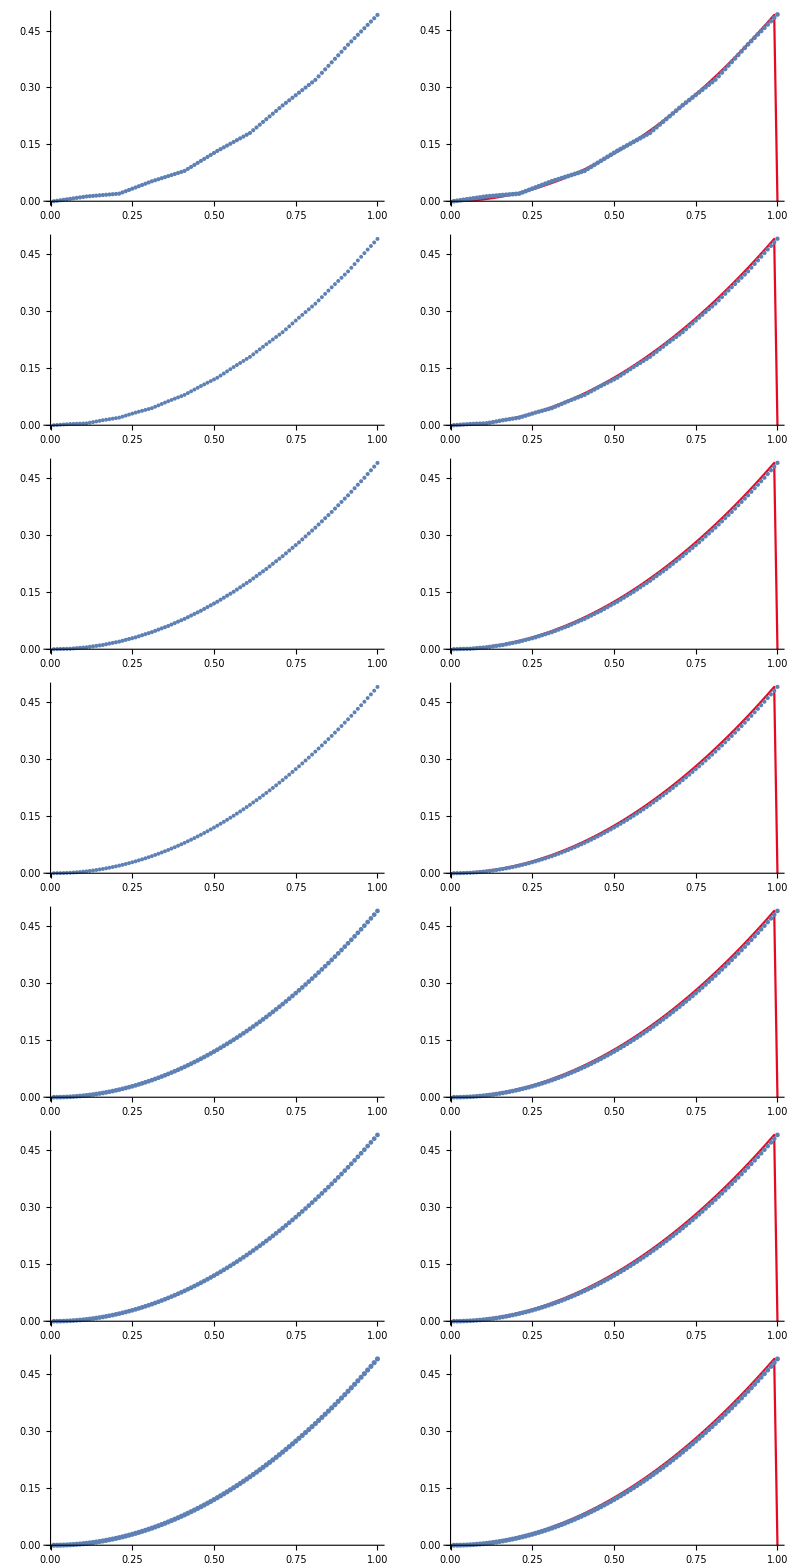
(-Graphics-)

```mathematica
(*记录误差*)
error=Table[{0,0,0,0},{i,7}];
imglist=Table[{0,0},{i,7}];
For[l=0,l<7,l++,
Clear[n,he1,he2,A,k];
(*离散程度*)
n=2^l*10;
tao=1-2 epsilon Log[n];
he1=tao/n;
he2=(1-tao)/n;
(*系数矩阵*)(*右侧向量*)
A=Table[0,{i,2 n-1},{j,1,2 n-1}];
fa=Table[0,{i ,2 n-1}];
For[k=1,k<n-1,k++,
A[[k,k]]=2 epsilon /he1;
A[[k,k+1]]=-epsilon/he1+1/2;
A[[k+1,k]]=-epsilon/he1-1/2;
fa[[k]]=k he1^2;
A[[k+n,k+n]]=2 epsilon /he2;
A[[k+n,k+n+1]]=-epsilon/he2+1/2;
A[[k+1+n,k+n]]=-epsilon/he2-1/2;
fa[[k+n]]=k he2^2+tao he2
];
k=n-1;
A[[k,k]]=2 epsilon /he1;
A[[k,k+1]]=-epsilon/he1+1/2;
A[[k+1,k]]=-epsilon/he1-1/2;
fa[[k]]=k he1^2;
A[[k+n,k+n]]=2 epsilon /he2;
fa[[k+n]]=k he2^2+tao he2;
k=n;
A[[k,k]]=epsilon /he1+epsilon /he2;
A[[k,k+1]]=-epsilon/he2+1/2;
A[[k+1,k]]=-epsilon/he2-1/2;
fa[[k]]=he1/2+(1-2 tao)/6/n/n;
(*求解方程组*)
ua=N[Inverse[N[A,50]].fa,50];
(*1000等分求解模最大误差*)
real=N[Table[u[i delta],{i,0,100}],50];
ns=Table[uh[n,epsilon,ua,i delta],{i,0,100}];
error[[l+1,1]]=Max[Abs[N[real-ns,15]]];
(*生成相关图像*)
table=Table[{i delta,ns[[i]]},{i,0,100}];
img1=ListPlot[table];
imglist[[l+1,1]]=img1;
imglist[[l+1,2]]=Show[img,img1];
(*复化3点gauss求解L1范数误差*)
delta2=N[1/8,50];
xi=Table[m delta2,{m,0,8}];
error[[l+1,3]]=N[Sum[5/18 (xi[[i+1]]-xi[[i+1]])*Abs[u[(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,epsilon,ua,(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]]+4/9 (xi[[i+1]]-xi[[i]])*Abs[u[(xi[[i+1]]+xi[[i]])/2]-uh[n,epsilon,ua,(xi[[i+1]]+xi[[i]])/2]]+5/18 (xi[[i+1]]-xi[[i]])*Abs[u[(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,epsilon,ua,(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]],{i,1,8}],15]
]
imglist//MatrixForm
```

```mathematica
(*求收敛阶*)
For[l=2,l≤7,l++,  
error[[l,2]]=Log[error[[l-1,1]]/error[[l,1]]]/Log[2];
error[[l,4]]=Log[error[[l-1,3]]/error[[l,3]]]/Log[2]];
list=Table[{10 2^i,error[[i+1,1]],error[[i+1,2]]},{i,0,6}];
list[[1,3]]="-";
PrependTo[list,{"n","无穷范数误差","Order"}];
GridBox[list,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | 无穷范数误差 | Order
10 | 0.00761205322595219 | -
20 | 0.00197786716933556 | 1.9443401093774
40 | 0.000456409636827301 | 2.1155443813249
80 | 0.000115430538365625 | 1.9833042989643
160 | 0.0000288980991779652 | 1.9979784494421
320 | 7.11999333201016×10^-6 | 2.0210268049087
640 | 1.66654163691573×10^-6 | 2.0950185278594

```mathematica
list1=Import["E:\\study_materials\\Finite Element Method\\Program\\Pg3\\code\\shinshkin.txt","Table"];
PrependTo[list1,{"n","L无穷误差","Order","L1误差","Order"}];
GridBox[list1,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
(*PrependTo[list2,{"n","L无穷误差","Order","L1误差","Order","L2误差","Order"}];
GridBox[list2,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm*)
```

n | L无穷误差 | Order | L1误差 | Order
10 | 0.00761205 | 0 | 0.00463937 | 0
20 | 0.00197787 | 1.94434 | 0.0011973 | 1.95415
40 | 0.000508034 | 1.96095 | 0.000306148 | 1.96748
80 | 0.000128696 | 1.98096 | 0.0000774368 | 1.98314
160 | 0.0000321524 | 2.00097 | 0.0000194711 | 1.99168
320 | 7.93629×10^-6 | 2.01839 | 4.90752×10^-6 | 1.98827
640 | 1.87313×10^-6 | 2.08302 | 1.28345×10^-6 | 1.93497